| Estimate | Standard Error | t-Statistic | P-Value
a | 60.4803 | 0.71544 | 84.5358 | 1.64176×10^-21
b | 52.0653 | 0.173661 | 299.81 | 9.42207×10^-30

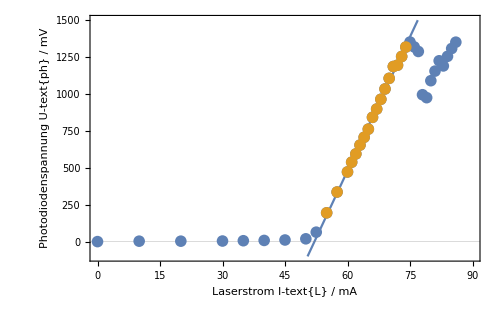

```mathematica
data=Import[NotebookDirectory[]<>"Kennlinie.txt","Table"];
data={#[[1]],#[[2]]+109}&/@data;
fitdata=Drop[Drop[data,9],-12];
nlm=NonlinearModelFit[fitdata,a (x - b),{a,b},x];
nlm["ParameterTable"]
plot=Show[Plot[Normal[nlm],{x,40,100},Frame->True,ImageSize->500,PlotRange->{{0,90},{-100,1500}},GridLines->{{},{0}},FrameLabel->{"Laserstrom I-text{L} / mA","Photodiodenspannung U-text{ph} / mV"}],ListPlot[{data,fitdata}]]
```

```mathematica
Export["/home/moritz/FP2/0407-Optisches Pumpen/img/part1/Kennlinie.pdf",plot]
```

/home/moritz/FP2/0407-Optisches Pumpen/img/part1/Kennlinie.pdf